Mathematica Project ___ ___ _

    
    Name : Jonah Patinkin     Course and Section : Math 151
    
    Date : 10/10/17      T.A. Yicong Huang

Exercise :
      Useing Mathematica we will find the x-interval that will linearly approximate 
      f(x)=  1/(x^2+2) at a=2 to the accuracies of 0.1, 0.01, 0.001. We will also use the quadratic expression of f(x) and compare lengths of intervals quadratic to linear approximation  

 Statement of Problem :
      Given the function, for decreasing values of accuracy starting at accuracy = 0.1 down to 0.001 we want to find the linear aproximation at a = 2. Then we need to make a conjecture as to what the lengths of quadratic to linear approximation are
    
 Method of Solution :
      First we use Mathematica to graph the linear approximation
      The graph helps us visualize the linear approixamtion at a = 2
      Then we use Mathematica to graph different linear aproximations at the accuracies 0.1,0.01,0.001
      The linear approximation falls within a certain interval closest to the graphs based on the given accuracies.
      We finally analyze the interval on which the linear aproximation is closest to the graphs.
      
  Conclusion :
       Mathematica' s output indicates that the linear aproximation for the quadratic expression is greater then the aproximation for the linear aproximation graphs

```mathematica
Math-151-03-Project-2-Fall-2017
Due October 10, 2017
Determining an interval for x throughout which a Tangential Approximation provides a specified accuracy for Sin(x).
```

```mathematica
Define the function f(x) and the center a of the neighborhood of approximation, then find the linear approximation linapprox:
```

```mathematica
f[x_]:=Sin[x]
a:=0
linapprox=f[a]+f'[a](x-a);
```

```mathematica
Print["Near x = ", a,", ",f[x], "≈ ",linapprox]
```

Near x = 0, Sin[x]≈ x

```mathematica
Draw the graphs of f(x) and linapprox:
```

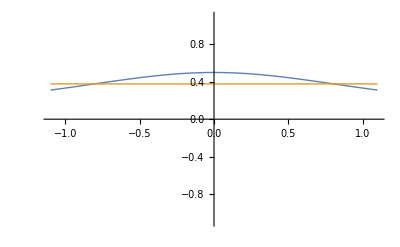

```mathematica
Plot[{f[x], linapprox},{x,-1.1,1.1},PlotRange->{-1.1,1.1}, PlotStyle->{Thick,Thick}]
```

```mathematica
Zooming out we get:
```

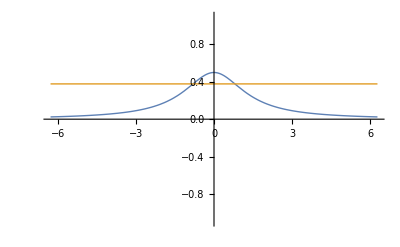

```mathematica
Plot[{f[x], linapprox},{x,-2Pi,2Pi},PlotRange->{-1.1,1.1}, PlotStyle->{Thick,Thick}]
```

```mathematica
Next we draw the graphs of the three functions, f(x)-accuracy, linapprox, and f(x)+accuracy
```

```mathematica
accuracy=0.1;
```

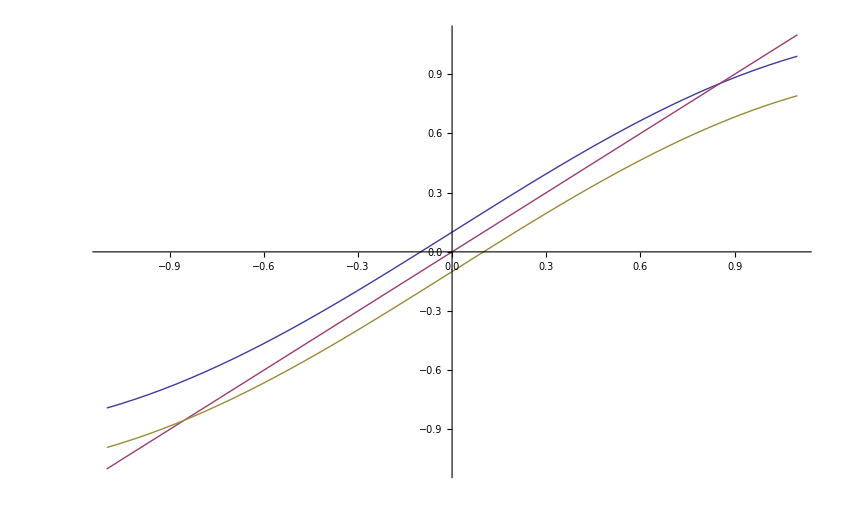

```mathematica
Plot[{f[x]+accuracy, linapprox, f[x]-accuracy},{x,-1.1,1.1},PlotRange->{-1.1,1.1}]
```

```mathematica
We up the accuracy , cut it in half,and draw the graphs again using new window, which is found by trial and error:
```

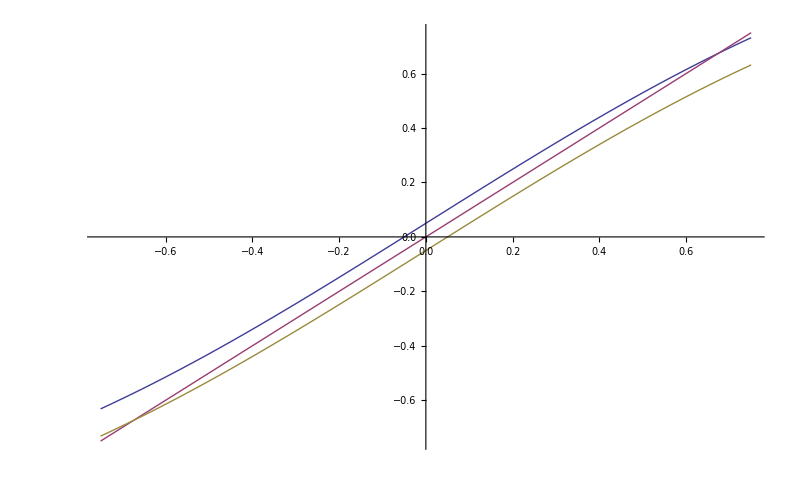

```mathematica
Plot[{f[x]+accuracy/2, linapprox, f[x]-accuracy/2},{x,-0.75,0.75},PlotRange->{-0.75,0.75}]
```

```mathematica
Upping the accuracy further and redrawing we get:
```

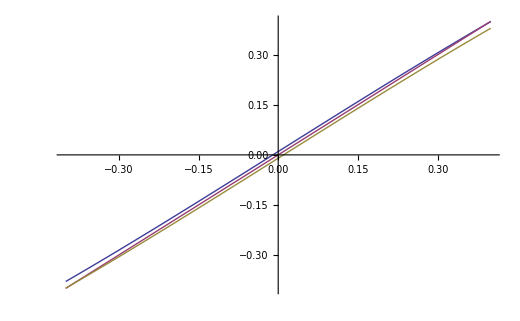

```mathematica
Plot[{f[x]+accuracy/10, linapprox, f[x]-accuracy/10},{x,-0.4,0.4},PlotRange->{-0.4,0.4}]
```

```mathematica
Lets reduce the accuracy one last time and try to get the interval:
```

```mathematica
Plot[{f[x]+accuracy/100, linapprox, f[x]-accuracy/100},{x,-0.06,0.06},PlotRange->{-0.05,0.05}]
```

-Graphics-

```mathematica
As you can see, it is difficult to see the interval or the x-coordinates of the points of intersection, unless we enlarge the graph by pulling at the corner squares in the frame, which we get by clicking the graph.
So we try to solve the equation: f(x)+ accuracy/100=linapprox:
```

```mathematica
Solve[linapprox- (f[x]+accuracy/100)==0,x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-0.001+x-Sin[x]==0,x]

```mathematica
We failed.Indeed Mathematica failed us!  Let's try the lower graph
```

```mathematica
Solve[linapprox- (f[x]-accuracy/100)==0,x]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[0.001+x-Sin[x]==0,x]
```

Solve::ivar: 0.1 is not a valid variable.

Solve[False,0.1]

```mathematica
Here too Mathematica failed us. 
No worry, we can play a "trick" on Mathematica. Here it is:
We know that solving f(x)=g(x) is the same as finding the x-intercept(s) of the graph of y=f(x)-g(x).So we find the the x-intercept(s) of the graph of y=f(x)-g(x)
```

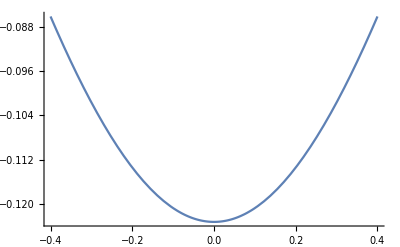

```mathematica
Plot[linapprox-(f[x]+accuracy/100),{x,-0.4,0.4}]
```

```mathematica
It worked! We can now read off the x-intercept which happens to be the x-coordinate of the point of intersection of the graphs of linapprox and f(x)+accuracy/100.
The other point of intersection is found as follows:
```

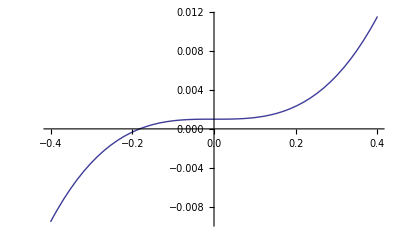

```mathematica
Plot[linapprox-(f[x]-accuracy/100),{x,-0.4,0.4}]
```

```mathematica
The last two graphs show us that the desired interval is x=-.18 (from last graph) to x=.18 (from prior graph).
```

```mathematica
*************************************************************
************************************************************

Here's another example:
```

(8 x^2)/((4-x^2)^3)+2/((4-x^2)^2)

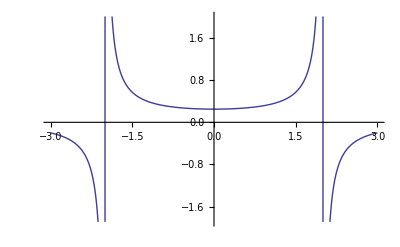

1/3+2/9 (-1+x)

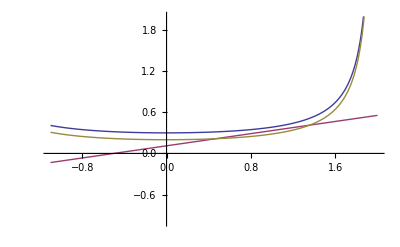

```mathematica
f[x_]:=1/(4-x^2)
Plot[f[x],{x,-3,3}]
a:=1
linapprox=f[a]+f'[a](x-a)
Plot[{f[x]+0.05, linapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2}]
```

-Graphics-

1/3+2/9 (-1+x)+7/27 (-1+x)^2

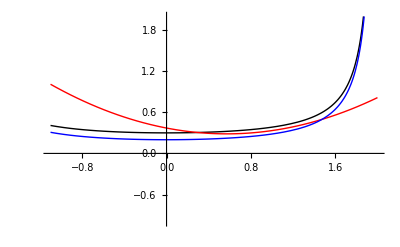

```mathematica
(* A higher degree approximation than a straight line is a parabolic approximation given by: 
quadraticapprox = f[a]+f'[a](x-a)+(1/2)f''(a)(x-a).
Using such an approximation, we approximate our function f(x)=1/(4-x^2)at a = 1  *)

f[x_]:=1/(4-x^2)
Plot[f[x],{x,-3,3}]
a:=1
quadraticapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},PlotStyle->{Black,Red,Blue}]
```

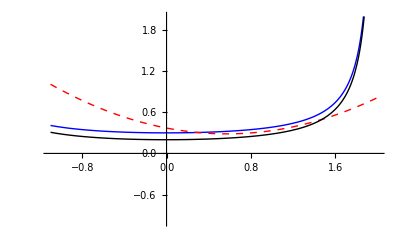

```mathematica
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Directive[Thick,Dashed]],Directive[Black, Thick]}]
```

-Graphics-

1/3+38/81 (-1+x)+7/27 (-1+x)^2

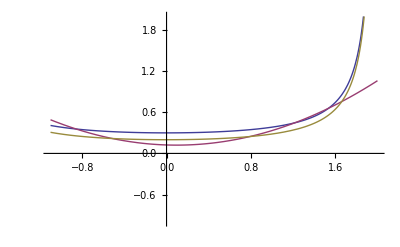

```mathematica
f[x_]:=1/(4-x^2)
Plot[f[x],{x,-3,3}]
a:=1
cubicapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2+(1/3!)f'''[a](x-a)
Plot[{f[x]+0.05, cubicapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2}]
```

```mathematica
******The next two examples is for your own fun and information!
```

-Graphics-

1/3+38/81 (-1+x)+7/27 (-1+x)^2

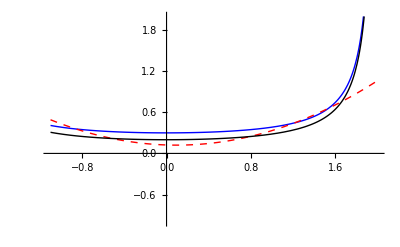

```mathematica
f[x_]:=1/(4-x^2)
Plot[f[x],{x,-3,3}]
a:=1
cubicapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2+(1/3!)f'''[a](x-a)
Plot[{f[x]+0.05, cubicapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},PlotStyle->{Directive[Blue,Thick],Directive[Red,Directive[Thick,Dashed]],Directive[Black, Thick]}]
```

-Graphics-

1/3+38/81 (-1+x)+7/27 (-1+x)^2

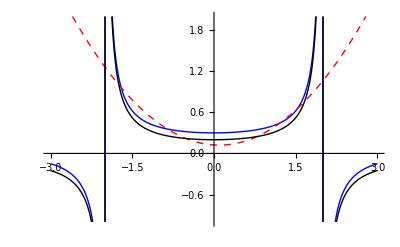

```mathematica
f[x_]:=1/(4-x^2)
Plot[f[x],{x,-3,3}]
a:=1
cubicapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2+(1/3!)f'''[a](x-a)
Plot[{f[x]+0.05, cubicapprox, f[x]-0.05},{x,-3,3},PlotRange->{-1,2},PlotStyle->{Directive[Blue,Thick],Directive[Red,Directive[Thick,Dashed]],Directive[Black, Thick]}]
```

```mathematica
Exercises
1. Use Mathematica to find the x-interval that will linearly approximate 
      f(x)=  1/(x^2+2) at a=2to the following 3 cases of accuracy:

      (i)0.1
           (ii)0.01
and (iii) 0.001

2. Repeat Exercise 1 above using quadratic approximation. 

3.In each case, compare the  lengths of intervals(estimate their size using the graphs)as follows: 
        quadratic approximation to linear approximation.
```

```mathematica
f[x_]:=1/(x^2+2)
a := 2
linapprox = f[a]+f'[a](x-a)
```

0.377778

```mathematica
Plot[{f[x], linapprox},{x,-1.1,1.1},PlotRange->{-1.1,1.1}, PlotStyle->{Thick,Thick}]
```

```mathematica
Print["Near x = ", a,", ",f[x], "≈ ",linapprox]
```

Near x = 2, 0.497512≈ 0.377778

```mathematica
accuracy=0.1;

Plot[{f[x]+accuracy, linapprox, f[x]-accuracy},{x,-1.1,1.1},PlotRange->{-1.1,1.1}]
```

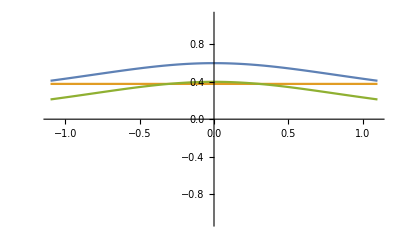
```mathematica
-Graphics-

Plot[{f[x]+accuracy/2, linapprox, f[x]-accuracy/2},{x,-0.75,0.75},PlotRange->{-0.75,0.75}]
```

```mathematica
Plot[{f[x]+accuracy/10, linapprox, f[x]-accuracy/10},{x,-0.4,0.4},PlotRange->{-0.4,0.4}]
```

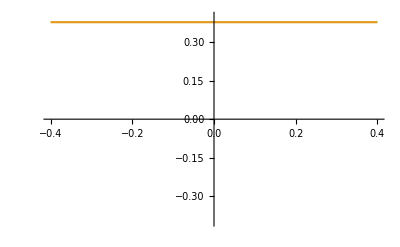
```mathematica
-Graphics-

Plot[{f[x]+accuracy/100, linapprox, f[x]-accuracy/100},{x,-0.06,0.06},PlotRange->{-0.05,0.05}]
```

```mathematica
-Graphics-

Plot[linapprox-(f[x]+accuracy/100),{x,-0.4,0.4}]
```

```mathematica
Plot[linapprox-(f[x]-accuracy/100),{x,-0.4,0.4}]
```

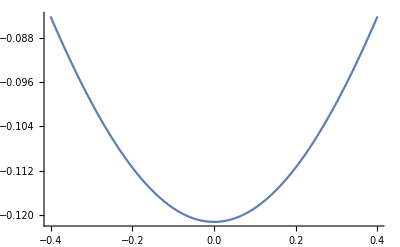
```mathematica
-Graphics-


Plot[{f[x]+0.05, linapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2}]
```

-Graphics-

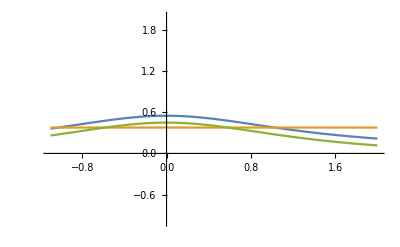

-Graphics-

linear aproximation closest to (-1,1)

```mathematica
quadraticapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},PlotStyle->{Black,Red,Blue}]
```

0.544907

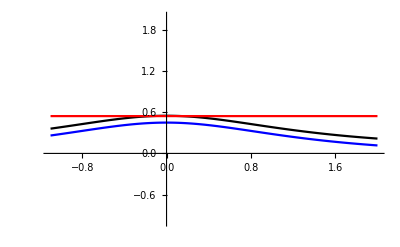

```mathematica
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Directive[Thick,Dashed]],Directive[Black, Thick]}]
```

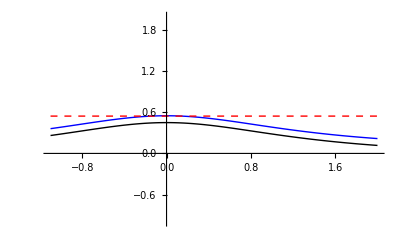

-Graphics-

```mathematica
InverseFunction[f[x]]
```

InverseFunction[0.497512]

```mathematica
accuracy=0.01;
Print["Near x = ", a,", ",f[x], "≈ ",linapprox]
```

Near x = 2, 0.497512≈ 0.377778

```mathematica
Plot[{f[x]+accuracy, linapprox, f[x]-accuracy},{x,-1.1,1.1},PlotRange->{-1.1,1.1}]
```

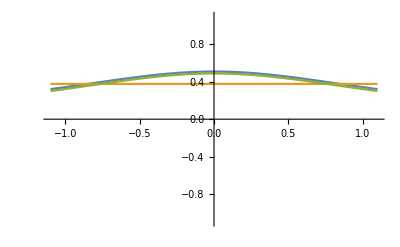

```mathematica
Plot[{f[x]+accuracy/2, linapprox, f[x]-accuracy/2},{x,-0.75,0.75},PlotRange->{-0.75,0.75}]
```

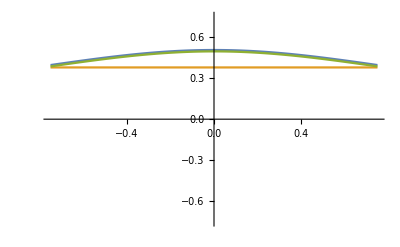

-Graphics-

```mathematica
Plot[{f[x]+accuracy/10, linapprox, f[x]-accuracy/10},{x,-0.4,0.4},PlotRange->{-0.4,0.4}]
```

```mathematica
Plot[{f[x]+accuracy/100, linapprox, f[x]-accuracy/100},{x,-0.06,0.06},PlotRange->{-0.05,0.05}]
```

```mathematica
Plot[linapprox-(f[x]+accuracy/100),{x,-0.4,0.4}]
```

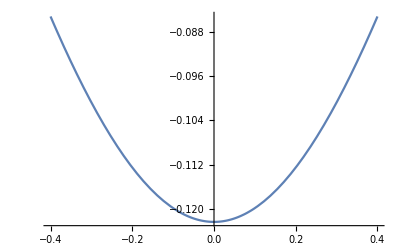

```mathematica
Plot[linapprox-(f[x]-accuracy/100),{x,-0.4,0.4}]
```

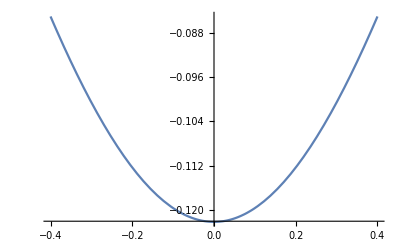
```mathematica
-Graphics-

Plot[{f[x]+0.05, linapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2}]







quadraticapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},PlotStyle->{Black,Red,Blue}]
```

-Graphics-

-Graphics-

0.544907

-Graphics-

0.544907

-Graphics-

```mathematica
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Directive[Thick,Dashed]],Directive[Black, Thick]}]
```

```mathematica
accuracy=0.001;
Print["Near x = ", a,", ",f[x], "≈ ",linapprox]
```

Near x = 2, 0.497512≈ 0.377778

```mathematica
Plot[{f[x]+accuracy, linapprox, f[x]-accuracy},{x,-1.1,1.1},PlotRange->{-1.1,1.1}]
```

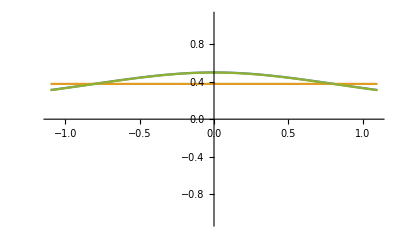
```mathematica
-Graphics-
Plot[{f[x]+accuracy/2, linapprox, f[x]-accuracy/2},{x,-0.75,0.75},PlotRange->{-0.75,0.75}]
```

```mathematica
Plot[{f[x]+accuracy/10, linapprox, f[x]-accuracy/10},{x,-0.4,0.4},PlotRange->{-0.4,0.4}]
```

```mathematica
Plot[{f[x]+accuracy/100, linapprox, f[x]-accuracy/100},{x,-0.06,0.06},PlotRange->{-0.05,0.05}]
```

```mathematica
Plot[linapprox-(f[x]+accuracy/100),{x,-0.4,0.4}]
```

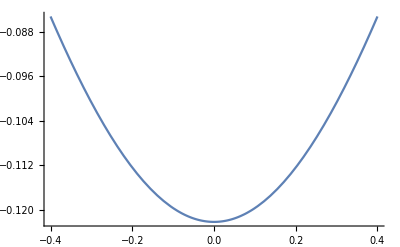
```mathematica
-Graphics-
Plot[linapprox-(f[x]-accuracy/100),{x,-0.4,0.4}]
```

```mathematica
-Graphics-



Plot[{f[x]+0.05, linapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2}]



quadraticapprox=f[a]+f'[a](x-a)+(1/2)f''[a](x-a)^2
Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},PlotStyle->{Black,Red,Blue}]
```

-Graphics-

-Graphics-

0.544907

-Graphics-

0.544907

```mathematica
-Graphics-

Plot[{f[x]+0.05, quadraticapprox, f[x]-0.05},{x,-1.1,2},PlotRange->{-1,2},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Directive[Thick,Dashed]],Directive[Black, Thick]}]
```